```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# Input Mesh

## Region

```mathematica
Ω=RegionDifference[Rectangle[],Disk[{0,0},1/2]];
```

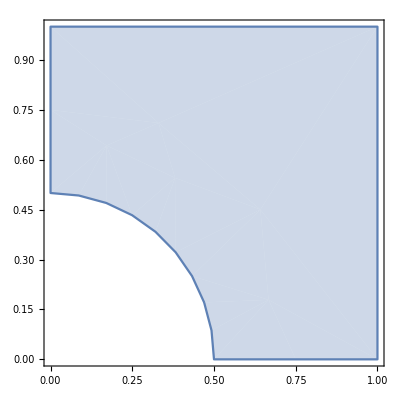

```mathematica
RegionPlot@Ω
```

## Mesh

```mathematica
<<NDSolve`FEM`
```

```mathematica
𝒵=ToElementMesh[Ω,"MaxCellMeasure"-> .3,"MeshOrder"->1,"MeshElementType"->TriangleElement];
nodes=𝒵[[1]];
triangles=𝒵[[2,1,1]]-1;
neighbors=𝒵["ElementConnectivity"][[1]]-1;
Export["nodes.dat",Prepend[nodes,Length@nodes]];
Export["triangles.dat",Prepend[triangles,Length@triangles]];
Export["neighbors.dat",neighbors];
```

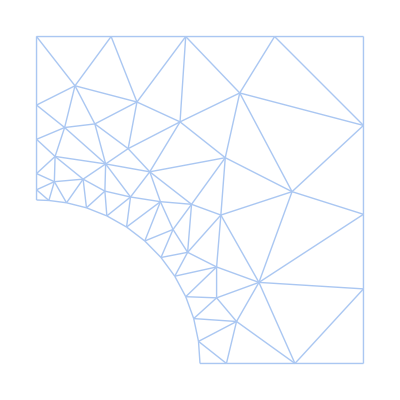

```mathematica
HighlightMesh[MeshRegion@𝒵,(*Labeled[1,"Index"]*)None,PlotTheme->"Lines"]
```